==========================================================

Analyzing Twin Director Fields from Anti-Analytic f(zbar)

==========================================================

1. Input Function f(zbar) = Cos[zbar/2]

In Cartesian (x,y): f(x,y) = Cos[x/2] Cosh[y/2]+ⅈ Sin[x/2] Sinh[y/2]

Anti-analyticity check 2*d_z(f) (should be 0): 0

2. Constructed Director Fields (n1 and n2):

n1(x,y) = 1/2 ⅈ (Cos[x/2] Cosh[y/2] √(-1+8/(Cos[x]+Cosh[y]))-Sin[x/2] Sinh[y/2])+1/2 (-Cos[x/2] Cosh[y/2]-√(-1+8/(Cos[x]+Cosh[y])) Sin[x/2] Sinh[y/2])

n2(x,y) = 1/2 ⅈ (Cos[x/2] Cosh[y/2] √(-1+8/(Cos[x]+Cosh[y]))+Sin[x/2] Sinh[y/2])+1/2 (Cos[x/2] Cosh[y/2]-√(-1+8/(Cos[x]+Cosh[y])) Sin[x/2] Sinh[y/2])

Unit length check: |n1|^2 = 1 , |n2|^2 = 1

Difference check: n2 - n1 = Cos[1/2 (x-ⅈ y)]

3. Computing and Comparing Curvature Fields w1 and w2:

w1 = 2*d_z(n1) = (4 ⅈ Cos[1/2 (x-ⅈ y)]^2 Sin[1/2 (x+ⅈ y)])/(√(8-Cos[x]-Cosh[y]) (Cos[x]+Cosh[y])^(3/2))

w2 = 2*d_z(n2) = (4 ⅈ Cos[1/2 (x-ⅈ y)]^2 Sin[1/2 (x+ⅈ y)])/(√(8-Cos[x]-Cosh[y]) (Cos[x]+Cosh[y])^(3/2))

Real part of (w1 - w2): 0

Imaginary part of (w1 - w2): 0

SUCCESS! w1 and w2 are IDENTICAL (w1 == w2) while n1 != n2!

4. Plotting n1, n2, and Shared Curvature w:

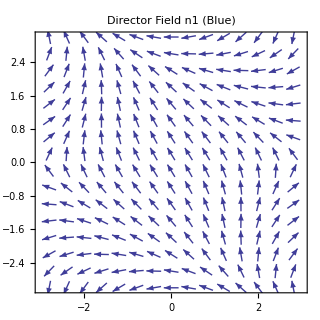
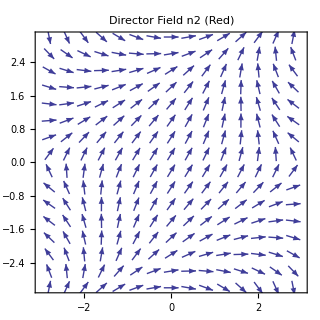
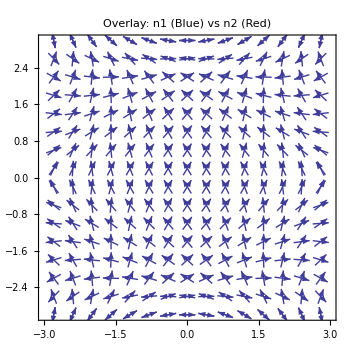

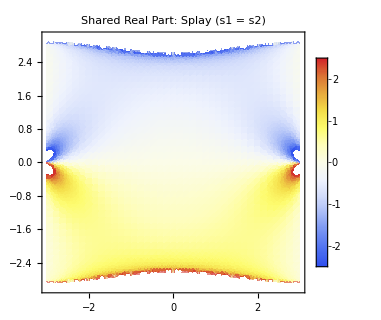
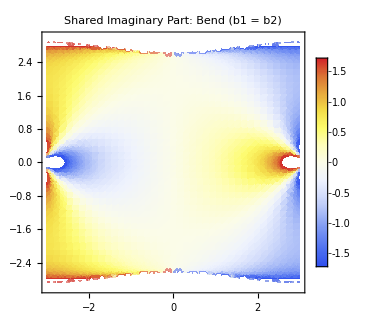

```mathematica
ClearAll["Global`*"];

(* ==========================================================*)
(*שלב 1:הגדרת אופרטורי וירטינגר ופונקציות עזר*)
(* ==========================================================*)
twoDz[g_]:=D[g,x]-I*D[g,y];
twoDzbar[g_]:=D[g,x]+I*D[g,y];

conj[expr_]:=ComplexExpand[Conjugate[expr],TargetFunctions->{Re,Im}];
absSq[expr_]:=Simplify[ComplexExpand[Re[expr]^2+Im[expr]^2]];

(* ==========================================================*)
(*שלב 2:הפונקציה שמקבלת f אנטי-אנליטית,משווה w ומציירת n*)
(* ==========================================================*)
AnalyzeTwinDirectors[fExpr_,plotLim_?NumericQ,exampleName_String]:=Module[{fxy,antiAnalyticErr,u,v,rhoSq,rho,domainAssumptions,n1x,n1y,n2x,n2y,n1,n2,norm1,norm2,w1,w2,wDiff,realDiffW,imagDiffW,splay1,bend1,plotN1,plotN2,plotBothN,plotS,plotB,baseDir,outputDir,summaryText,nbFile},Print[Style["==========================================================",Bold,14,Blue]];
Print[Style["Analyzing Twin Director Fields from Anti-Analytic f(zbar)",Bold,16,Blue]];
Print[Style["==========================================================",Bold,14,Blue]];
(*א.מעבר לקואורדינטות (x,y) ובדיקה ש-f אכן אנטי-אנליטית*)fxy=ComplexExpand[fExpr/. zbar->(x-I*y)];
antiAnalyticErr=FullSimplify[ComplexExpand[twoDz[fxy]],Assumptions->{x∈Reals,y∈Reals}];
Print[Style["1. Input Function f(zbar) = ",Bold,14,Darker[Blue]],fExpr];
Print["   In Cartesian (x,y): f(x,y) = ",fxy];
Print["   Anti-analyticity check 2*d_z(f) (should be 0): ",antiAnalyticErr];
(*ב.חילוץ החלק הממשי u,החלק המדומה v והאמפליטודה rho= |f|*)u=ComplexExpand[Re[fxy]];
v=ComplexExpand[Im[fxy]];
rhoSq=FullSimplify[u^2+v^2,Assumptions->{x∈Reals,y∈Reals}];
rho=Sqrt[rhoSq];
domainAssumptions={x∈Reals,y∈Reals,rhoSq>0,rhoSq<4};
(*ג.בנייה ישירה של הרכיבים הממשיים של n1 ו-n2 (ללא סיבוכי ComplexExpand)*)n1x=FullSimplify[-u/2-v*Sqrt[4-rhoSq]/(2*rho),Assumptions->domainAssumptions];
n1y=FullSimplify[-v/2+u*Sqrt[4-rhoSq]/(2*rho),Assumptions->domainAssumptions];
n2x=FullSimplify[+u/2-v*Sqrt[4-rhoSq]/(2*rho),Assumptions->domainAssumptions];
n2y=FullSimplify[+v/2+u*Sqrt[4-rhoSq]/(2*rho),Assumptions->domainAssumptions];
n1=n1x+I*n1y;
n2=n2x+I*n2y;
norm1=FullSimplify[n1x^2+n1y^2,Assumptions->domainAssumptions];
norm2=FullSimplify[n2x^2+n2y^2,Assumptions->domainAssumptions];
Print["\n",Style["2. Constructed Director Fields (n1 and n2):",Bold,14,Darker[Blue]]];
Print["   n1(x,y) = ",n1];
Print["   n2(x,y) = ",n2];
Print["   Unit length check: |n1|^2 = ",norm1," , |n2|^2 = ",norm2];
Print["   Difference check: n2 - n1 = ",FullSimplify[n2-n1,Assumptions->domainAssumptions]];
(*ד.חישוב w1 ו-w2 והשוואה אלגברית ביניהם*)Print["\n",Style["3. Computing and Comparing Curvature Fields w1 and w2:",Bold,14,Darker[Blue]]];
w1=FullSimplify[ComplexExpand[twoDz[n1]],Assumptions->domainAssumptions];
w2=FullSimplify[ComplexExpand[twoDz[n2]],Assumptions->domainAssumptions];
wDiff=w1-w2;
realDiffW=FullSimplify[ComplexExpand[Re[wDiff]],Assumptions->domainAssumptions];
imagDiffW=FullSimplify[ComplexExpand[Im[wDiff]],Assumptions->domainAssumptions];
Print["   w1 = 2*d_z(n1) = ",w1];
Print["   w2 = 2*d_z(n2) = ",w2];
Print["   Real part of (w1 - w2): ",realDiffW];
Print["   Imaginary part of (w1 - w2): ",imagDiffW];
If[realDiffW===0&&imagDiffW===0,Print[Style["   SUCCESS! w1 and w2 are IDENTICAL (w1 == w2) while n1 != n2!",Bold,15,Darker[Green]]],Print[Style["   WARNING: w1 and w2 differ. Check if f is anti-analytic.",Bold,15,Red]]];
(*ה.שרטוט הגרפים של n1,n2 ושל הספליי והבנד המשותפים*)Print["\n",Style["4. Plotting n1, n2, and Shared Curvature w:",Bold,14,Darker[Blue]]];
plotN1=VectorPlot[{n1x,n1y},{x,-plotLim,plotLim},{y,-plotLim,plotLim},PlotLabel->Style["Director Field n1 (Blue)",Bold,13],VectorStyle->Blue,VectorColorFunction->None,VectorScale->{Tiny,Automatic,None},ImageSize->320];
plotN2=VectorPlot[{n2x,n2y},{x,-plotLim,plotLim},{y,-plotLim,plotLim},PlotLabel->Style["Director Field n2 (Red)",Bold,13],VectorStyle->Red,VectorColorFunction->None,VectorScale->{Tiny,Automatic,None},ImageSize->320];
plotBothN=Show[plotN1,plotN2,PlotLabel->Style["Overlay: n1 (Blue) vs n2 (Red)",Bold,13],ImageSize->350];
Print[Row[{plotN1,plotN2,plotBothN},Spacer[10]]];
splay1=FullSimplify[D[n1x,x]+D[n1y,y],Assumptions->domainAssumptions];
bend1=FullSimplify[D[n1y,x]-D[n1x,y],Assumptions->domainAssumptions];
plotS=DensityPlot[splay1,{x,-plotLim,plotLim},{y,-plotLim,plotLim},PlotLabel->Style["Shared Real Part: Splay (s1 = s2)",Bold,13],ColorFunction->"TemperatureMap",PlotLegends->Automatic,PlotPoints->40,ImageSize->320];
plotB=DensityPlot[bend1,{x,-plotLim,plotLim},{y,-plotLim,plotLim},PlotLabel->Style["Shared Imaginary Part: Bend (b1 = b2)",Bold,13],ColorFunction->"TemperatureMap",PlotLegends->Automatic,PlotPoints->40,ImageSize->320];
Print[Row[{plotS,plotB},Spacer[20]]];
(*ו.שמירה אוטומטית של כל הקבצים וה-Notebook בתיקייה*)baseDir=Quiet@Check[NotebookDirectory[],Directory[]];
outputDir=FileNameJoin[{baseDir,exampleName}];
If[!DirectoryQ[outputDir],CreateDirectory[outputDir]];
Export[FileNameJoin[{outputDir,exampleName<>"_Director_n1.png"}],plotN1,ImageResolution->300];
Export[FileNameJoin[{outputDir,exampleName<>"_Director_n2.png"}],plotN2,ImageResolution->300];
Export[FileNameJoin[{outputDir,exampleName<>"_Overlay_n1_n2.png"}],plotBothN,ImageResolution->300];
Export[FileNameJoin[{outputDir,exampleName<>"_Shared_Splay_s.png"}],plotS,ImageResolution->300];
Export[FileNameJoin[{outputDir,exampleName<>"_Shared_Bend_b.png"}],plotB,ImageResolution->300];
summaryText=StringJoin["==========================================================\n","הסבר ופירוט הערכים בדוגמה: ",exampleName,"\n","==========================================================\n\n","1. הפונקציה האנטי-אנליטית שנבחרה (f[zbar]):\n   ","f(zbar) = ",ToString[fExpr,InputForm],"\n   ","f(x, y) = ",ToString[fxy,InputForm],"\n   ","בדיקת אנטי-אנליטיות 2*d_z(f) = ",ToString[antiAnalyticErr,InputForm],"\n\n","2. ריבוע האמפליטודה (|f|^2 = rho^2):\n   ","rho^2(x, y) = ",ToString[rhoSq,InputForm],"\n\n","3. שדה הדירקטור הראשון (n1 = n1x + I*n1y):\n   ","n1(x, y) = ",ToString[n1,InputForm],"\n\n","4. שדה הדירקטור השני (n2 = n2x + I*n2y):\n   ","n2(x, y) = ",ToString[n2,InputForm],"\n\n","5. שדה העקמומיות מ-n1 (w1 = 2*d_z(n1)):\n   ","w1(x, y) = ",ToString[w1,InputForm],"\n\n","6. שדה העקמומיות מ-n2 (w2 = 2*d_z(n2)):\n   ","w2(x, y) = ",ToString[w2,InputForm],"\n\n","7. השוואה בין w1 ל-w2 (w1 - w2):\n   ","Real Error (s1 - s2) = ",ToString[realDiffW,InputForm],"\n   ","Imaginary Error (b1 - b2) = ",ToString[imagDiffW,InputForm],"\n\n","8. החלק הממשי המשותף - התבדרות (Splay, s):\n   ","s(x, y) = ",ToString[splay1,InputForm],"\n\n","9. החלק המדומה המשותף - כיפוף (Bend, b):\n   ","b(x, y) = ",ToString[bend1,InputForm],"\n"];
Export[FileNameJoin[{outputDir,exampleName<>"_Explanation_and_Values.txt"}],summaryText,"Text",CharacterEncoding->"UTF-8"];
nbFile=FileNameJoin[{outputDir,exampleName<>"_Notebook.nb"}];
Quiet@Check[NotebookSave[EvaluationNotebook[],nbFile],Null];
Print[Style["\nנשמר בהצלחה! התיקייה עם כל התמונות וה-Notebook נמצאת בנתיב:\n"<>outputDir,Bold,14,Darker[Green]]];];

(* ==========================================================*)
(*שלב 3:הרצה על דוגמה 1 (עם חלון שרטוט-3 עד 3 בתוך הדיסקה)*)
(* ==========================================================*)
Rval=5;
AnalyzeTwinDirectors[Cos[zbar/2],3,"Twin_Directors_Cos_2"];
```